```mathematica
NUnit=8;
NVertical=6;
Frequency = 2.2*10^6;

Omega = 2*π*Frequency;
LBZ = 27*10^-6;
L0A=5.6*10^-6;
L0B = 27*10^-6;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
alpha = -Omega/(Omega^2*L0A);
Alpha = Omega/(Omega^2*LBZ)
beta = -Omega/(Omega^2*L0B);
betaZ =  -Omega/(Omega^2*LBZ);
LBZControl = 1/(Omega*LBZ);

symmShift = If[NVertical==6,-1,0];
```

0.00267938

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_,kz_}]:=N[(-(CAz-Alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz+Alpha) Cos[ky] X[3]]
```

```mathematica
xcords=Join[Subdivide[0,Pi,4],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1]];

ycords=Join[Subdivide[0,0,4],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[0,0,4-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1]];

zcords=Join[Subdivide[0,0,4*4],Subdivide[2Pi/NVertical,Pi,NVertical/2-1],Subdivide[Pi,Pi,4*4-1]];

pathTheoretical=Table[{xcords[[i]],ycords[[i]],zcords[[i]]},{i,1,Length[xcords]}];
```

```mathematica
LowerBandPathValsTheory=Table[Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];
UpperBandPathValsTheory=Table[-Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];

BandsTheory = Table[SortBy[120.5*{UpperBandPathValsTheory[[i]],LowerBandPathValsTheory[[i]]},Re],{i,1,Length[pathTheoretical]}];
```

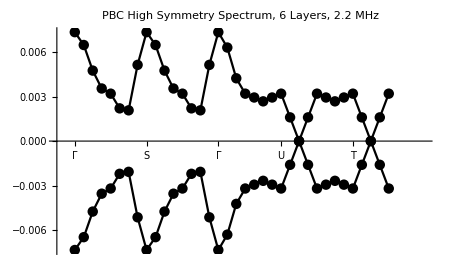
-Graphics-Hamiltonian Eigenvalues E_n

```mathematica
Labeled[ListLinePlot[{BandsTheory[[;;,1]],BandsTheory[[;;,2]]},Mesh->All,PlotRange->{{-1,40},Automatic},PlotLabel->"PBC High Symmetry Spectrum, "<>ToString[8+2*symmShift]<> " Layers, "<>ToString[Frequency/(10^6)]<>" MHz",PlotStyle->{Black,Black},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{21+symmShift,"Z"},{25+symmShift,"U"},{29+symmShift,"R"},{33+symmShift,"T"},{37+symmShift,"Z"}},Automatic},ImageSize->450],{"","Hamiltonian Eigenvalues E_n"},{Bottom,Left},RotateLabel->True]
```